## Definiciones. (correr celda)

```mathematica
fs=FullSimplify;
mf=MatrixForm;
prod=KroneckerProduct;
id=IdentityMatrix;
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
n={nx,ny,nz};
s={sx,sy,sz};
daga=ConjugateTranspose;

b[1]=Flatten[prod[{1,0},{1,0}]](*|00>*);
b[2]=Flatten[prod[{1,0},{0,1}]](*|01>*);
b[3]=Flatten[prod[{0,1},{1,0}]](*|10>*);
b[4]=Flatten[prod[{0,1},{0,1}]](*|11>*);
```

```mathematica
Parte II: problema 1
```

```mathematica
(*Computo explicito del operador de rotacion de un qubit al rededor del eje n*)
R[θ_,nx_,ny_,nz_]=MatrixExp[-I θ/2 n.s]/.{nx^2+ny^2+nz^2-> 1}//fs;
R[θ,nx,ny,nz]//mf
```

(Cos[θ/2]-ⅈ nz Sin[θ/2] | (-ⅈ nx-ny) Sin[θ/2]
(-ⅈ nx+ny) Sin[θ/2] | Cos[θ/2]+ⅈ nz Sin[θ/2])

```mathematica
(*En terminos de angulos de euler*)
R[α,0,0,1].R[β,0,1,0].R[γ,0,0,1]//fs//mf
```

(ⅇ^(-1/2 ⅈ (α+γ)) Cos[β/2] | -ⅇ^(-1/2 ⅈ (α-γ)) Sin[β/2]
ⅇ^(1/2 ⅈ (α-γ)) Sin[β/2] | ⅇ^(1/2 ⅈ (α+γ)) Cos[β/2])

#### Parte IIProblema 2

```mathematica
x=I R[π,1,0,0];
y=I R[π,0,1,0];
z=I R[π,0,0,1];
h=I R[π,1/(√2),0,1/(√2)];

Print[x//mf,y//mf,z//mf,h//mf]
```

(0 | 1
1 | 0)(0 | -ⅈ
ⅈ | 0)(1 | 0
0 | -1)(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

```mathematica
Print[x.z.x//mf,x.y.x//mf,h.x.h//mf,
h.z.h//mf]
```

(-1 | 0
0 | 1)(0 | ⅈ
-ⅈ | 0)(1 | 0
0 | -1)(0 | 1
1 | 0)

#### PArte II. Problema 3 (lo hice en papel)

#### Parte II. Poblema 4

```mathematica
(*Para ver que pasa, construyo el operador de evolucion para un hamiltoniano de interaccion entre dos espines de heisenberg y lo aplico sobre los estados de dos cubits*)
Clear[HH]
Sx[1]=prod[sx,id[2]]/2;
Sy[1]=prod[sy,id[2]]/2;
Sz[1]=prod[sz,id[2]]/2;
Sx[2]=prod[id[2],sx]/2;
Sy[2]=prod[id[2],sy]/2;
Sz[2]=prod[id[2],sz]/2;
HH=Sx[1].Sx[2]+Sy[1].Sy[2]+Sz[1].Sz[2];
U[t_]=MatrixExp[-I t HH]//fs; (*operador swap a menos de una fase?*)
```

```mathematica
b[1]=Flatten[prod[{1,0},{1,0}]](*|00>*);
b[2]=Flatten[prod[{1,0},{0,1}]](*|01>*);
b[3]=Flatten[prod[{0,1},{1,0}]](*|10>*);
b[4]=Flatten[prod[{0,1},{0,1}]](*|11>*);
U[π].b[1]
U[π].b[2]//fs
U[π].b[3]//fs
U[π].b[4]
```

{ⅇ^(-(ⅈ π)/4),0,0,0}

{0,0,-(-1)^(3/4),0}

{0,-(-1)^(3/4),0,0}

{0,0,0,ⅇ^(-(ⅈ π)/4)}

```mathematica
(*recordatorio de QCNOT*)
QCNOT=prod[{{1,0},{0,0}},id[2]]+prod[{{0,0},{0,1}},sx]
QCNOT.QCNOT
MatrixExp[-I t QCNOT]
%/.t-> π/2
%/-I//mf
```

{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

{{ⅇ^(-ⅈ t),0,0,0},{0,ⅇ^(-ⅈ t),0,0},{0,0,Cos[t],-ⅈ Sin[t]},{0,0,-ⅈ Sin[t],Cos[t]}}

{{-ⅈ,0,0,0},{0,-ⅈ,0,0},{0,0,0,-ⅈ},{0,0,-ⅈ,0}}

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

#### Parte III

#### Problema 1 (e)

```mathematica
(*rutina para obtener los coeficientes en la expansion: *)
(*inicializo variables*)
rA={r1A,r2A,r3A};
rB={r1B,r2B,r3B};
J={{J11,J12,J13},{J21,J22,J23},{J31,J32,J33}};
expand[ρin_,rAin_,rBin_,Jin_]:=Module[{ρ=ρin,rA=rAin,r1B=rBin,J=Jin,rho,out},

(*asi se expande la matriz densidad mas general*)
rho=1/4(id[4]+prod[Sum[rA[[i]]s[[i]],{i,1,3}],id[2]]+
prod[id[2],Sum[rB[[i]]s[[i]],{i,1,3}]]+
Sum[J[[i]][[j]]prod[s[[i]],s[[j]]],{i,1,3},{j,1,3}]);

list={};
AppendTo[list,{rA,rB,Flatten[J]}];
varlist=Flatten[list];
sol=Solve[ρ==rho,varlist] (*igualo la matriz densidad dada a la expresion general*)
;
out=sol[[1]]
]
```

```mathematica
(*inciso (i)*)
bell1=(b[1]+b[4])/(√2);
ρ1=prod[bell1,bell1]

expand[ρ1,rA,rB,J]
```

{{1/2,0,0,1/2},{0,0,0,0},{0,0,0,0},{1/2,0,0,1/2}}

{r1A→0,r2A→0,r3A→0,r1B→0,r2B→0,r3B→0,J11→1,J12→0,J13→0,J21→0,J22→-1,J23→0,J31→0,J32→0,J33→1}

```mathematica
(*inciso (ii)*)
psi2=(b[2]-b[3])/√2;
ρ2=prod[psi2,psi2]
expand[ρ2,rA,rB,J]
```

{{0,0,0,0},{0,1/2,-1/2,0},{0,-1/2,1/2,0},{0,0,0,0}}

{r1A→0,r2A→0,r3A→0,r1B→0,r2B→0,r3B→0,J11→-1,J12→0,J13→0,J21→0,J22→-1,J23→0,J31→0,J32→0,J33→-1}

#### Parte III. Problema 2

```mathematica
psi=(b[2]-b[3])/√2;
ρpsi=prod[psi,psi];
ρ=x ρpsi+(1-x) 1/4 id[4];
Tr[ρ]
Eigenvalues[ρ]
Solve[ρ.ρ-ρ==0,x]
```

1

{(1-x)/4,(1-x)/4,(1-x)/4,1/4 (1+3 x)}

{{x→1}}

#### Pate III. Problema 2 (d): Bell’s inequality

```mathematica
psi=(b[2]-b[3])/√2;
ρpsi=prod[psi,psi];
ρ=x ρpsi+(1-x) 1/4 id[4];
Q=prod[sz,id[2]];
R=prod[sx,id[2]];
S=-(prod[id[2],sz]+prod[id[2],sx])/√2;
T=(prod[id[2],sz]-prod[id[2],sx])/√2;
Print[Eigenvalues[Q],Eigenvalues[R],Eigenvalues[S],Eigenvalues[T]]
(*solo puedo medir +-1, como en la desigualdad de bell *)
```

{-1,-1,1,1}{-1,-1,1,1}{-1,-1,1,1}{-1,-1,1,1}

```mathematica
(*violacion de la desigualdad de Bell usando el estado de Bell:*)
psi.(Q.S+R.S+R.T-Q.T).psi
```

2 √2

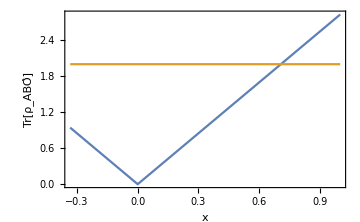

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-1/(√2)},{x→1/(√2)}}

```mathematica
(*Usando el operador densidad dependiente de x, defino*)
f[x_]:=Abs[Tr[ρ.(Q.S+R.S+R.T-Q.T)]]
(*el dominio de f es xϵ[-1/3,1]*)
Plot[{f[x],2},{x,-1/3,1},Frame->True,
FrameLabel->{"x","Tr[ρ_ABÔ]"},
FrameStyle->Directive[Black,16]]
Solve[f[x]==2,x](*se viola la desigualdad de Bell para xϵ(1/(√2),1)*)
```

```mathematica
Parte III. Problema 2 (e,f)
```

ρ^t_A=((1-x)/4 | 0 | 0 | -x/2
0 | (1+x)/4 | 0 | 0
0 | 0 | (1+x)/4 | 0
-x/2 | 0 | 0 | (1-x)/4)

1/8 (-4+Abs[1-3 x]+3 Abs[1+x])

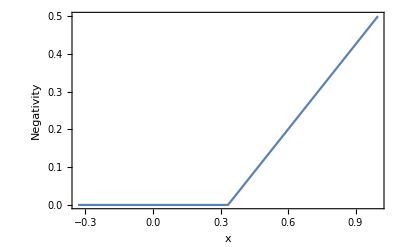

```mathematica
Clear[b]
b[1]=Flatten[prod[{1,0},{1,0}]](*|00>*);
b[2]=Flatten[prod[{1,0},{0,1}]](*|01>*);
b[3]=Flatten[prod[{0,1},{1,0}]](*|10>*);
b[4]=Flatten[prod[{0,1},{0,1}]](*|11>*);
trasArho=x/2(prod[b[2],b[2]]-prod[b[4],b[1]]-prod[b[1],b[4]]+prod[b[3],b[3]])+
(1-x)/4 id[4];
Print["ρ^t_A=",trasrho//mf//fs]
ev=Eigenvalues[trasArho];

(*Negatividad: (-1)* suma de los autovalores negativos de trasArho *)
Negativity[x_]=Sum[(Abs[ev[[i]]]-ev[[i]])/2,{i,1,Length[ev]}]//fs
Plot[Negativity[x],{x,-1/3,1},Frame->True,
FrameLabel->{"x","Negativity"},
FrameStyle->Directive[Black,16]]
(*recordar que para un sistema de 2qubits, N(ρ^Subscript[t, A])>0 implica que hay entrelazamiento
(o sea el criterio de peres es necesario y suficiente)*)
```

```mathematica
Solve[Negativity[x]==0.00001,x]
(*Resultado: hay entrelazamiento para 1/3<x<1 *)
```

{{x→-1.00001},{x→0.333347}}

#### Concurrencia y entropia de formacion

{1/4 √((-1+x)^2),1/4 √((-1+x)^2),1/4 √((-1+x)^2),1/4 √((1+3 x)^2)}

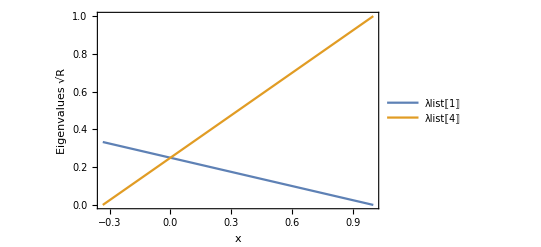

```mathematica
psi=(b[2]-b[3])/√2;
ρpsi=prod[psi,psi];
ρ=x ρpsi+(1-x) 1/4 id[4];
ρtilde=prod[sy,sy].ρ.prod[sy,sy] (*ρ tiene elementos reales, no hace falta conjugarla*);
R=ρtilde.ρ;
evR=Eigenvalues[R];
λlist={};
Do[AppendTo[λlist,Sqrt[evR[[i]]]],{i,1,Length[evR]}]
λlist
Plot[{λlist[[1]],λlist[[4]]},{x,-1/3,1},Frame->True,
PlotLegends->"Expressions",
FrameLabel->{"x","Eigenvalues √R"},
FrameStyle->Directive[Black,16]]
(*para x<0, el autovalor mas grande es el primero
para x>0, el mas grande es el ultimo
*)
```

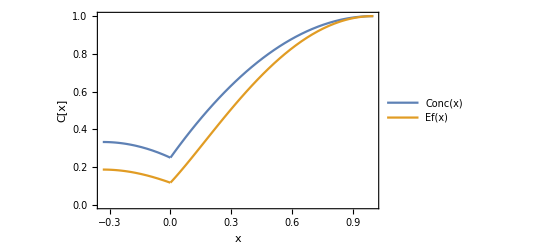

```mathematica
Clear[Conc]
Conc[x_]=Piecewise[{{2 λlist[[4]]-Tr[R]//fs,0<x<1},{2 λlist[[1]]-Tr[R]//fs,-1/3<x<0}}];
p1=(1+√(1-Conc[x]^2))/2;p2=(1-√(1-Conc[x]^2))/2;
Ef[x_]=-p1 Log2[p1]-p2 Log2[p2]//fs;
Plot[{Conc[x],Ef[x]},{x,-1/3,1},Frame->True,FrameLabel->{"x","C[x]"},
FrameStyle->Directive[Black,16],PlotLegends->"Expressions"]
```